Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

# Calculus 3 Equations and functions

```mathematica
=, :=and==Solve,NSolve,FindRoot,NRoots
Definition of functions (f[x_] and Function[x,]), Sum
Sin,Cos,Tan,Degree
Plot
ReplaceAll, /.
```

## Solving equations

We already encountered the symbols = and : = for assigning names to expressions or values to variables. However, for equations Mathematica uses a different symbol, namely the double equal-sign = =. For the solution of equations we have the command Solve for exact solutions and NSolve for numerical approximations. Besides, the command NRoots can be used for a polynomial equation. As you can read in the help information about Solve and NSolve, you can specify variables for which the equation(s) should be solved, or which should be eliminated. You can also try to let Mathematica solve several equations simultaneously.

```mathematica
?Solve
```

```mathematica
?NSolve
```

```mathematica
?NRoots
```

### Examples

```mathematica
Solve[x^2-5 x+6==0,x]
```

{{x→2},{x→3}}

As you can see, the output is a list of lists of so-called assignment-rules. So you can easily refer to one of the solutions with the help of [[ ]]. In order to show this it turns out to be convenient to give the equation a name, say quad.

```mathematica
quad=Solve[x^2-5 x+6==0,x]
```

Now the second solution can be referred to as

```mathematica
quad⟦2⟧
```

Or, if we only need the value of the second solution, then we should point to the 2nd part of the 1st part of the 2nd solution.

```mathematica
quad⟦2,1,2⟧
```

We can also ask for a symbolic solution of the general quadratic equation 
a*x^2 + b*x + c = 0. This should indeed give the abc-formula.

```mathematica
abcformula=Solve[a x^2+b x+c==0,x]
```

(Note: don't forget to insert space or * between a and x, and b and x)

Or, if you are more familiar to the pq-formula:

```mathematica
pqformula=Solve[x^2+p x+q==0,x]
```

Next we try to solve more complicated equations. We define equ1 and equ2 as polynomial equations of degree 4, i.e. the greatest power of x is 4.

```mathematica
fourth1=Expand[3 (1-x)^2 (x+2) (x-3)]
```

```mathematica
equ1=fourth1==0
```

```mathematica
Solve[equ1,x]
```

This result is not surprising. But, now have a look at the following:

```mathematica
fourth2=x^4-2 x+1
```

```mathematica
equ2=fourth2==0
```

```mathematica
Solve[equ2,x]
```

As you can see, Mathematica  is able to compute  exact solutions, but there are also some solutions that are not "real" in the sense that they do not belong to the set of real numbers. These are called complex solutions, that are elements of the set of so-called complex numbers. These can be recognized as containing the symbol ⅈ (which is properly the number with square equal to -1, so ⅈ^2 = -1). We will not dig deeper into this subject. In order to get a better idea of the numerical values of these solutions, we can ask for numerical approximations.

```mathematica
NSolve[equ2,x]
```

But, as we saw, Mathematica is able to determine exact solutions for equations of degree 4. So it has an algorithm for it, a kind of abcde-formula:

```mathematica
Solve[a x^4+b x^3+c x^2+d x+e==0,x]
```

In present mathematics this is the end: there is no general formula for the exact solution of polynomial equations of degree higher than 4. Hence, here we have to use the numerical approximation.

```mathematica
Solve[x^5-x^2+1==0,x]
```

```mathematica
NSolve[x^5-x^2+1==0,x]
```

Using NRoots, we get another output format:

```mathematica
NRoots[x^5-x^2+1==0,x]
```

These polynomial equations are rather simple, but some (a lot!) equations cannot even be solved numerically! For example exponential functions may be problematic. We can solve the following:

```mathematica
Solve[7^x==3,x]
```

But the following is a serious problem:

```mathematica
NSolve[7^x==Sin[x],x]
```

Remark (repeat):
If you ever use a decimal number in an equation, then Solve will always give numerical solutions. It is even enough to use a dot after an integer.

```mathematica
Solve[x^5-x^2+1.==0,x]
```

## Defining functions and finding zeros

### Definition of a function

Functions are usually defined with the help of : =, because we want the (delayed) evaluation only at the moment, that we need the function value. In the definition the argument of the function is put between brackets [ ] and is followed by an underscore, only in the lefthand side! For example we define a quadratic function.

```mathematica
fquad[x_]:=x^2-5 x+6
```

You will get no output (except maybe a message if you use of a name that is quite similar to an well-known name), because we only defined the function with the delayed assignment : =. But each time we ask for this function, it will be evaluated. At the argument position we may put every name or value we want (always without underscore!).

```mathematica
fquad[u]
```

6-5 u+u^2

```mathematica
fquad[4]
```

2

```mathematica
fquad[flower]
```

6-5 flower+flower^2

```mathematica
fquad[fquad[flower]]
```

6-5 (6-5 flower+flower^2)+(6-5 flower+flower^2)^2

```mathematica
Simplify[fquad[fquad[fquad[u]]]]
```

6-5 (12-35 u+32 u^2-10 u^3+u^4)+(12-35 u+32 u^2-10 u^3+u^4)^2

Another way to define a function is the  so-called "pure, or anonymous, function definition". Here we use the command Function. The advantage can be, that you do not need a name to define a function in this way (the function is "anonymous").

```mathematica
?Function
```

```mathematica
fquad2:=Function[x,x^2-4]
```

```mathematica
fquad2[u]
```

-4+u^2

Or, even:

```mathematica
Function[x,x^2-4][u]
```

-4+u^2

An example of a function of two variables:

```mathematica
f2:=Function[{x,y},x y^2-4]
```

```mathematica
f2[u,v]
```

-4+u v^2

```mathematica
f2[3,4]
```

44

### The zeros (or roots) of a function

Of course we can use Solve and NSolve for the determination of zeros of a function, as it is solving an equation.

```mathematica
Solve[fquad[x]==0,x]
```

{{x→2},{x→3}}

Or, solving a two variable-equation for one of the variables:

```mathematica
Solve[f2[x,y]==0,x]
```

{{x→4/y^2}}

However, it is not always as easy as this!

```mathematica
Clear[f]
```

```mathematica
f[x_]:=ⅇ^x-x-2
```

```mathematica
Solve[f[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2-ProductLog[-1/ⅇ^2]},{x→-2-ProductLog[-1,-1/ⅇ^2]}}

```mathematica
NSolve[f[x]==0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.84141},{x→1.14619}}

If even NSolve does not give solutions, then the FindRoot command is a last option. This is an approximation based on the so-called Newton-method, which is an algorithm using intersections of tangent lines to the graph of the function with the x-axis.

```mathematica
?FindRoot
```

In order to be able to choose an appropriate starting value a plot may be useful. A function of one variable can be plotted with Plot. Also several functions of one variable can be presented in one graph..

```mathematica
?Plot
```

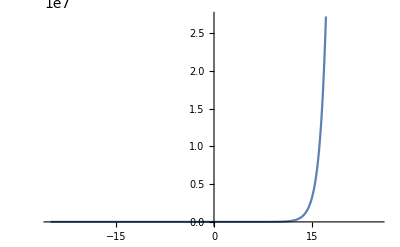

```mathematica
Plot[f[x],{x,-25,25}]
```

Of course we have to choose an appropriate range for the argument x, in order to see where the function value is zero. Let us try another range:

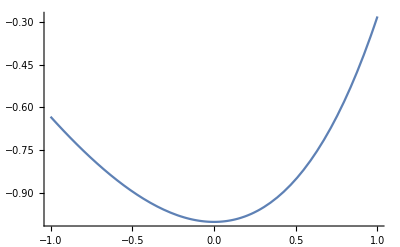

```mathematica
Plot[f[x],{x,-1,1}]
```

Not good. A new attempt:

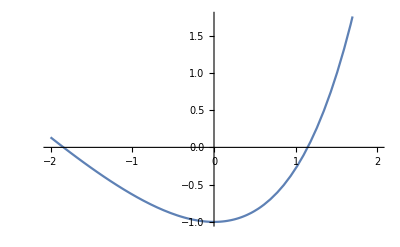

```mathematica
Plot[f[x],{x,-2,2}]
```

Here we can see two zeros. Mind, that we are not sure that these are all the zeros. Only a precise anaysis of the function can give this certainty. Let us try to find the zeros in the graph by choosing starting points for the FindRoot-command that seem to be appropriate..

```mathematica
FindRoot[f[x]==0,{x,1}]
```

{x→1.14619}

```mathematica
FindRoot[f[x]==0,{x,-2}]
```

{x→-1.84141}

Another way to see the zeros for this function is searching the intersection points of the functions g(x) = E^x and the function h(x) = x+2. Plotting two functions in one picture is as easy as plotting one function.

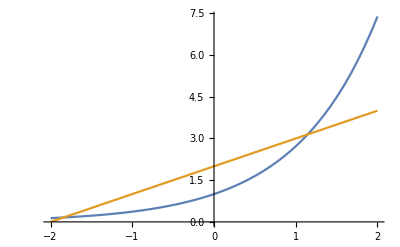

```mathematica
Plot[{ⅇ^x,x+2},{x,-2,2}]
```

### The sum of some function values

In Mathematica it is easy to evaluate a sum of function values.

```mathematica
?Sum
```

As an example let' s use the function fquad again:

```mathematica
fquad[x_]:=x^2-5 x+6
```

The sum of the first ten function values fquad(1)+fquad(2)+...+fquad(10) is:

```mathematica
Sum[fquad[x],{x,10}]
```

170

The following is a summation from 1 to 10 with step size 1/2, so fquad(1)+fquad(1.5)+fquad(2)+...+fquad(9.5)+fquad(10)

```mathematica
Sum[fquad[x],{x,1,10,1/2}]
```

1235/4

For function of two variables the Sum command can be extended in an obvious way:

```mathematica
f2:=Function[{x,y},x y^2-4]
```

```mathematica
Sum[f2[x,y],{x,1,2},{y,2,5}]
```

130

### Some special functions

Mathematica has a lot of built-in standard functions, e.g. the goniometric functions sine, cosine and tangent.

```mathematica
?Sin
```

```mathematica
?Cos
```

```mathematica
?Tan
```

Usually the units of the argument are radians. But you can also use degrees in the following way.

```mathematica
?Degree
```

```mathematica
N[180 °]
```

3.14159

```mathematica
N[π]
```

3.14159

```mathematica
Sin[π/6]
```

1/2

```mathematica
N[Sin[30 °]]
```

0.5

Plotting is easy with the Plot-command.

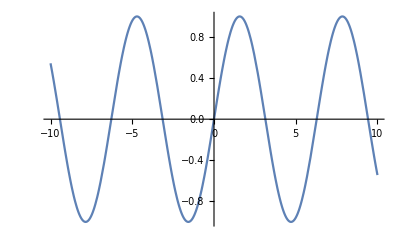

```mathematica
Plot[Sin[x],{x,-10,10}]
```

It is not possible to find all (infinitely many!) zeros of the function sine, but each zero can be approximated, using FindRoot with an appropriate starting value. For this the plot is very useful.

```mathematica
Solve[Sin[x]==0,x]
```

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

```mathematica
FindRoot[Sin[x]==0,{x,5}]
```

{x→9.42478}

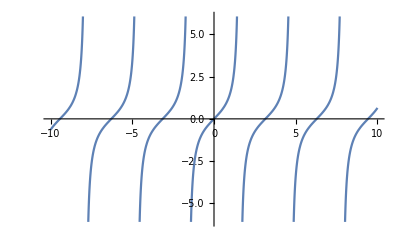

```mathematica
Plot[Tan[x],{x,-10,10}]
```

```mathematica
FindRoot[Tan[x]==0,{x,3}]
```

{x→3.14159}

## Replacement commands

Replacement is substitution according to one or more (assignment) rules. A rule is an assignment expression between braces { }, like {x→4}. A list of rules is for example {{x→2},{x→-6}}. You may recall a typical example of a list of rules, namely the output of the Solve and NSolve commands.

```mathematica
?ReplaceAll
```

```mathematica
?/.
```

As you can see, both commands have the same effect.

```mathematica
ReplaceAll[x^3-2 x^2,x->3]
```

9

```mathematica
x^3-2 x^2/.{x->3}
```

9

If we use the expression:

```mathematica
expr1=x^2-ⅇ^x
```

-ⅇ^x+x^2

then we can for example replace x by an other expression, like a+b:

```mathematica
expr1/.{x->a+b}
```

(a+b)^2-ⅇ^(a+b)

You may use replacement for a zero check.

```mathematica
equ1=-18+33 x-9 x^2-9 x^3+3 x^4==0
```

-18+33 x-9 x^2-9 x^3+3 x^4==0

```mathematica
zeros=Solve[equ1,x]
```

{{x→-2},{x→1},{x→1},{x→3}}

Now, substituting these zeros into the equ1 should give confirmations of being zeros. Indeed:

```mathematica
equ1/.zeros
```

{True,True,True,True}

## Exercises

1. 	Solve the equation x^4+3 x^3-7 x^2+6x-4=0. Which solutions are real? 
2. 	Try to solve the equation E^x=2-x^2. Make also one plot of both functions
	f(x)=E^x and g(x)=2-x^2 and observe, that the equation has two real 
	solutions. Find approximations for them, using the FindRoot command.
3. 	Plot the graphs of the functions f1(x)=x, f2(x)=-x and f3(x)=x*Sin(x) 
	in one picture on the interval [-π,π].
4. 	Make a plot of the function f(x)=x^5-8 x^4+11 x^3+56 x^2-180x+144. 
	Try to show all relevant points (esp. the zeros) of this function, 
	by varying the ranges for the argument x.
	Determine the zeros with Solve and check the solutions with the help of the replacement rule.
5.	Use Manipulate to solve the quadratic equations x^2+a x+1=0, 
	taking for a all integer values between 0 and 20.
Answers

Links to all notebooks

basicsDMDO
calc1 calc2 calc3 calc4 calc5
matrices
ode
odesys

```mathematica
NSolve[x^4+3x^3-7x^2+6x-4==0,x, Reals]
```

```mathematica
{{x->-4.768656724532064},{x->1.1557686726356218}}
Solve[ⅇ^x == 2-x^2, x]
Plot[ⅇ^x, 2-x^2]
```

{{x→-4.76866},{x→1.15577}}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

{x→-1.31597}

```mathematica
Plot[ⅇ^x,2-x^2, 1, 10]
```

Plot::nonopt: Options expected (instead of 10) beyond position 2 in Plot[ⅇ^x,2-x^2,1,10]. An option must be a rule or a list of rules.

```mathematica
Plot[{ⅇ^x,2-x^2},{x,-2,2}]
```

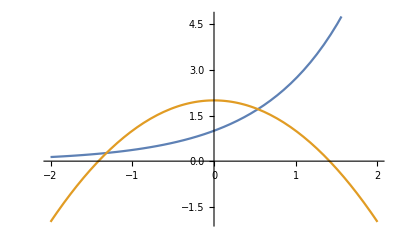
```mathematica
-Graphics-
FindRoot[ⅇ^x==2-x^2,{x,-1}]
```

-Graphics-

```mathematica
{x->-1.31597377779629}
FindRoot[ⅇ^x==2-x^2,{x,1}]
```

{x→-1.31597}

{x→0.537274}

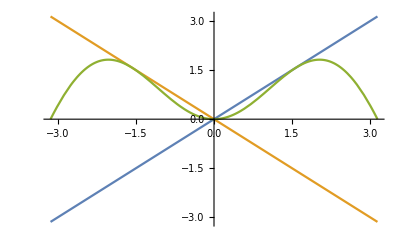

```mathematica
{x->0.5372744491738566}
Plot[{x, -x, x×Sin[x]},{x,-π,π}]
```

```mathematica
Plot[x^5-8 x^4+11 x^3+56 x^2-180x+144, {x,-5,5}]
solutions =Solve[x^5-8 x^4+11 x^3+56 x^2-180x+144==0,x]
```

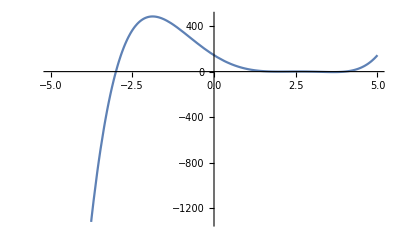
```mathematica
-Graphics-
x^5-8 x^4+11 x^3+56 x^2-180x+144/.solutions
```

-Graphics-

```mathematica
Manipulate[Solve[x^2+a x + 1==0,x], {a,0,20,1}]
```